# Notebook Documents

## Notebook Basics

tutorial/NotebooksAsDocuments

guide/NotebookBasics

guide/MenuItems

guide/NotebookShortcuts

### Text & Evaluation

A notebook can generally be be treated as a scratch-pad. We can mix text and code freely, as long as each is in a different cell.

#### Examples

##### Using Text cells

I am a text cell made with command-7

##### Using Input cells

```mathematica
"I am an input cell"
```

```mathematica
"I am an input cell made with command-9"
```

##### Using Code cells

```mathematica
"I am a code cell made with command 8"
```

#### Extra

##### Default Cell Styles

We can define what cell appears when we type in empty space by setting the DefaultNewCellStyle option on the head of a cell group or at the Notebook level.

For example we’ll make the default style a "Code" cell:

```mathematica
$groupHeader=Nest[PreviousCell,EvaluationCell[],3];
SetOptions[$groupHeader,DefaultNewCellStyle->"Code"];
```

Now when you type in this cell group the default style will be a code cell. You may have to create two cells before the front-end applies the change.

Then we’ll reset this. Note that most cell styles can be reset by using Inherited:

```mathematica
SetOptions[$groupHeader,DefaultNewCellStyle->Inherited];
```

##### Style Key Listings

Here’s a quick way to find the style shortcuts for the current notebook:

```mathematica
AssociationMap[
CurrentValue[EvaluationNotebook[],{
StyleDefinitions,
#,
MenuCommandKey
}]&,
Cases[Keys@FE`Evaluate[FEPrivate`GetPopupList["MenuListStyles"]],_String]
]//Dataset
```

### Sections, Subsections, and Grouping

When working through a project or when developing it’s good to provide structure to your documents. We do this via different cell types with different CellGroupingRules

#### Examples

##### Sample Layout

# Title (1)

## Subtitle

## Chapter (2)

Subchapter (3)

## Section (4)

### Subsection (5)

#### Subsubsection (6)

##### Subsubsubsection

Subsubsubsubsection

Item

Subitem

Subsubitem

Text

```mathematica
Code
```

```mathematica
Input
```

##### Making a to do list

#### To Do List

I am an item cell made with shift-8

I need to implement writing the rest of my talk

( FINISHED: 6/19/2017 )

#### Extra

##### Viewing All Layout Cells

This will view all the styles defined in the current notebook:

```mathematica
Cell[#,#]&/@Cases[Keys@FE`Evaluate[FEPrivate`GetPopupList["MenuListStyles"]],_String]//CellPrint
```

### Initialization Cells and Groups

There’s a system for auto-initializing code, called initialization cells. Mathematica will prompt us to evaluate them when we first evaluate something in a notebook

#### Examples

##### Making an initialization cell

Set with the menu

```mathematica
f[x_]:=x+1
```

##### Making an initialization group

Set on the group header cell

```mathematica
packageFunction1[]:="something";
```

```mathematica
pFunction2[]:="something else";
```

```mathematica
asd[]:=""
```

### Wolfram|Alpha Cells

Mathematica is integrated with Wolfram|Alpha and it is possible to get Wolfram|Alpha output directly in a notebook

#### Examples

##### Simple Wolfram|Alpha output

Make this with =

WolframAlphaQueryParseResults

```mathematica
Entity["Country","Germany"]//GeoGraphics
```

WolframAlphaQueryParseResults

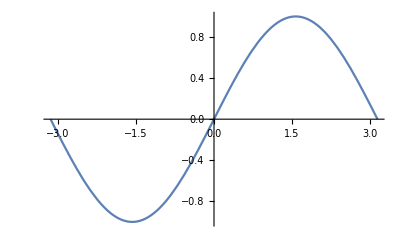

##### Full-report Wolfram|Alpha output

Make this with ==

Germany

WolframAlphaQueryResults

##### Inline Wolfram|Alpha output

Make this with control-=

```mathematica
plotCountry[country_]:=GeoGraphics[country]
```

```mathematica
plotCountry[LinguisticAssistant]
```

-Graphics-

### Notebook Files and Directories

If a notebook is saved its location is accessible from the notebook itself, and so resources can be organized relative to a notebook

#### Examples

##### Locating a file relative to a notebook

(We’ll try to find something exciting in the same directory as our notebook)

```mathematica
FileNameJoin@{NotebookDirectory[],"package.wl"}//SystemOpen
```

```mathematica
NotebookFileName[]
```

/Users/markb/Desktop/NotebookDocuments.nb

Locate notebooks relative to current notebook

```mathematica
FileNames["*.nb",NotebookDirectory[]]
```

{/Users/markb/Desktop/ExcitingNotebook.nb,/Users/markb/Desktop/NotebookDocuments.nb,/Users/markb/Desktop/Stylesheet Example.nb,/Users/markb/Desktop/WSSTemplates.nb}

```mathematica
FileNameJoin@{NotebookDirectory[],"ExcitingNotebook.nb"}//SystemOpen
```

### Inline Cells

An inline cell is when we embed one cell in another:

#### Examples

##### Creating a basic inline cell

This is a text cell This is an inline cell made with control -9

##### Inline cells in mathematical notation

(x^2+z)/2 inline cells are made automatically when formatting math

#### Extra

##### Changing Inline Cell Styles

We can change how new inline cells display with DefaultNewInlineCellStyle

```mathematica
SetOptions[EvaluationCell[],
DefaultNewInlineCellStyle->"Title"]This is inline, but looks like a title
```

##### Disabling Inline Cells

We can turn off inline cells

```mathematica
SetOptions[EvaluationCell[],AllowInlineCells->False];
(* Try to make a new inline cell in this cell *)
```

### Editing with Palettes

Palettes are notebooks that often server the purpose of making editing notebooks simpler

#### Examples

##### Making a big, blue cell with the basic writing assistant

(x^2+z)/2

### Editing via Code

The Wolfram Language has functionality for editing notebooks and cells at a basic level:

#### Examples

##### Fading a notebook in and out

(With the magic of WindowOpacity)

```mathematica
SetOptions[InputNotebook[],WindowOpacity->.5]
```

```mathematica
SetOptions[InputNotebook[],WindowOpacity->1]
```

```mathematica
SetOptions[InputNotebook[],WindowOpacity->#]&/@
Join[Range[1,0,-.1],Range[0,1,.1]];
```

##### Making cell text flash blue

Hi, I’m going to turn blue!

```mathematica
SetOptions[PreviousCell[],FontColor->Blue]
```

```mathematica
SetOptions[PreviousCell@PreviousCell[],FontColor->Inherited]
```

### Cell » Show Expression

We can view the contents of a cell in a notebook, and, if we need to, we can also edit cells by hand (but this should only really be done for quick, short chunks of code)

#### Examples

##### Viewing the contents of a cell

Hello

##### Changing the style of a cell

Hello

#### Extra

##### ToggleShowExpression

The ToggleShowExpression front end token does just what Cell » Show Expression does:

```mathematica
SelectionMove[EvaluationCell[],All,Cell];
FrontEndTokenExecute["ToggleShowExpression"]
```

### Creating Notebooks via Code

The Wolfram Language has support for making various kinds of notebooks via code

#### Examples

##### Creating a basic notebook

```mathematica
CreateDocument@{Graphics[Disk[]]}
```

xjyx4_shm429FrontEndObject[LinkObject["xjyx4_shm", 3, 1]]429Untitled-98

##### Creating a paste palette

```mathematica
CreatePalette@PasteButton["☺",ImageSize->200]
```

xjyx4_shm430FrontEndObject[LinkObject["xjyx4_shm", 3, 1]]430Untitled-99

I am happy “☺”

##### Creating a simple dialog

```mathematica
MessageDialog["Hello!"]
```

xjyx4_shm433FrontEndObject[LinkObject["xjyx4_shm", 3, 1]]433433

## Styling & Stylesheets

There is extensive documentation on how to use and build stylesheets. Most functionality is in the Format > Stylesheets menu

tutorial/WorkingWithStylesheets

guide/Stylesheets

guide/NotebookFormattingAndStyling

### Styled Notebooks

There’s a rich collection of built-in notebooks that have a given style or layout

#### Examples

##### Creating a notebook with a basic template

##### Creating a structured notebook

#### Extra

##### CreateNotebook

CreateNotebook is designed to open the various types of notebooks. For example it can open a notebook for a data repository submission.

```mathematica
CreateNotebook["DataResource"]
```

### Stylesheets

Every notebook has an associated stylesheet which can be accessed from the Format menu. Stylesheets are designed to cascade, much like CSS. Stylesheets are themselves notebooks

#### Examples

##### Applying a built-in stylesheet

##### Opening a notebook’s private stylesheet

Format > Edit Stylesheet

#### Extra

##### Stylesheet chains

We can traverse the inheritance chain for a stylesheet by clicking on the cell that defines the default styles.

### Stylesheet Editing and Style Cells

Cells can take myriad options and since style cells are simply cells, they can too (but they pass their options on):

#### Examples

##### Creating a basic style cell

##### Basic cell styling

##### Showing group openers

##### A more complex example

#### Extra

##### The Notebook style

Styles that should apply to a notebook generally can be put in the Notebook style cell. For example this cell will make the background of the notebook teal and make it semi transparent:

```mathematica
Cell[StyleData["Notebook"],
Background->Hue[.5,.5,.5],
WindowOpacity->.5
]
```

## Notebook Programming

#### Documentation

There is extensive documentation on working with notebooks and cells programmatically

tutorial/ManipulatingNotebooksOverview

tutorial/CellsAsWolframLanguageExpressions

tutorial/ManipulatingNotebooksFromTheKernel

tutorial/ManipulatingTheFrontEndFromTheKernel

### FrontEnd Objects & Expressions

Everything we see in the from end is either part of a Notebook, Cell, or Box, each of which has a special front-end object and expression form:

#### Examples

##### NotebookObject & Notebook expressions

##### CellObject & Cell expressions

##### BoxObject & Box expressions

### Notebook programming via the Kernel

The kernel can be used to do many types of basic notebook

#### Examples

##### Manipulating the current selection

##### Notebook reading and writing

##### Notebook opening, saving, closing, etc.

### Notebook programming via the FrontEnd

We can also manipulate notebooks via the front-end itself. We generally do this via front-end tokens and front-end packets, with the former being far more commonly used.

#### Examples

##### Copying and pasting a cell with front-end tokens

##### Converting a selection to input-text with front-end packets

##### Converting a selection to plain-text with the FE context